```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

4811

4492

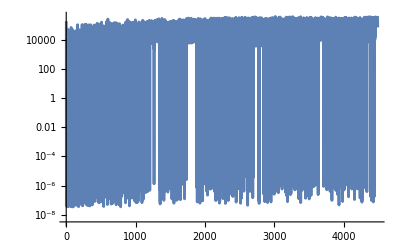

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
PlotRange->All,
Joined->True
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|L1PhaseSet→-24.3095,L2PhaseSet→-34.3622,Q1EkG→150.687,Q2EkG→-154.642,Q3EkG→112.071,Q4EkG→119.954,Q5EkG→-18.8265,Q6EkG→-137.86,S1ELkG→794.945,S2ELkG→-1805.22,S3ELkG→-1127.73,S3ERkG→-704.45,S2ERkG→-2543.64,S1ERkG→1007.12,Q5FFkG→-88.1306,Q4FFkG→-123.216,Q3FFkG→81.4879,Q2FFkG→136.804,Q1FFkG→-242.647,Q0FFkG→165.849,PDrive_mean_x→-0.0000192873,PDrive_mean_y→1.22×10^-8,PDrive_sigma_x→7.5963×10^-6,PDrive_sigma_y→0.00001545,PDrive_mean_xp→0.000545621,PDrive_mean_yp→-3.2856×10^-6,PDrive_sigmaSI90_x→6.0656×10^-6,PDrive_sigmaSI90_y→5.6185×10^-6,PDrive_emitSI90_x→0.0000179121,PDrive_emitSI90_y→6.1705×10^-6,PDrive_zLen→0.0000108682,PDrive_zCentroid→991.332,PWitness_mean_x→-0.0000367202,PWitness_mean_y→-1.3673×10^-6,PWitness_sigma_x→0.0000434206,PWitness_sigma_y→0.0000393687,PWitness_mean_xp→0.000526199,PWitness_mean_yp→0.0000104034,PWitness_sigmaSI90_x→0.0000363296,PWitness_sigmaSI90_y→0.0000361267,PWitness_emitSI90_x→0.000129362,PWitness_emitSI90_y→0.000177645,PWitness_zLen→0.0000680549,PWitness_zCentroid→991.332,bunchSpacing→-0.0000448668,transverseCentroidOffset→0.0000174874,lostChargeFraction→0.,maximizeMe→399072.|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L1PhaseSet : -24.3095464893
L2PhaseSet : -34.3622182608
Q1EkG : 150.687309354
Q2EkG : -154.6424560863
Q3EkG : 112.0710563764
Q4EkG : 119.9541128028
Q5EkG : -18.8264967091
Q6EkG : -137.860318635
S1ELkG : 794.9446419919
S2ELkG : -1805.2197786058
S3ELkG : -1127.7266606324
S3ERkG : -704.4501112534
S2ERkG : -2543.640992439
S1ERkG : 1007.1234946446
Q5FFkG : -88.1306313107
Q4FFkG : -123.2162199952
Q3FFkG : 81.487896229
Q2FFkG : 136.803619185
Q1FFkG : -242.647336689
Q0FFkG : 165.849328375
PDrive_mean_x : -0.0000192873
PDrive_mean_y : 1.22e-8
PDrive_sigma_x : 7.5963e-6
PDrive_sigma_y : 0.00001545
PDrive_mean_xp : 0.000545621
PDrive_mean_yp : -3.2856e-6
PDrive_sigmaSI90_x : 6.0656e-6
PDrive_sigmaSI90_y : 5.6185e-6
PDrive_emitSI90_x : 0.0000179121
PDrive_emitSI90_y : 6.1705e-6
PDrive_zLen : 0.0000108682
PDrive_zCentroid : 991.3318055047
PWitness_mean_x : -0.0000367202
PWitness_mean_y : -1.3673e-6
PWitness_sigma_x : 0.0000434206
PWitness_sigma_y : 0.0000393687
PWitness_mean_xp : 0.0005261988
PWitness_mean_yp : 0.0000104034
PWitness_sigmaSI90_x : 0.0000363296
PWitness_sigmaSI90_y : 0.0000361267
PWitness_emitSI90_x : 0.000129362
PWitness_emitSI90_y : 0.0001776445
PWitness_zLen : 0.0000680549
PWitness_zCentroid : 991.331760638
bunchSpacing : -0.0000448668
transverseCentroidOffset : 0.0000174874
lostChargeFraction : 0.
maximizeMe : 399072.0311227131

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

0.0000174874

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L1PhaseSet","L2PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG"}
]
```

{L1PhaseSet,L2PhaseSet,Q0FFkG,Q1EkG,Q1FFkG,Q2EkG,Q2FFkG,Q3EkG,Q3FFkG,Q4EkG,Q4FFkG,Q5EkG,Q5FFkG,Q6EkG,S1ELkG,S1ERkG,S2ELkG,S2ERkG,S3ELkG,S3ERkG}

```mathematica
fitVar = "PDrive_zLen"
```

PDrive_zLen

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVars,
Symbol[#]&/@freeVars
]
```

FittedModel[<<1>>]

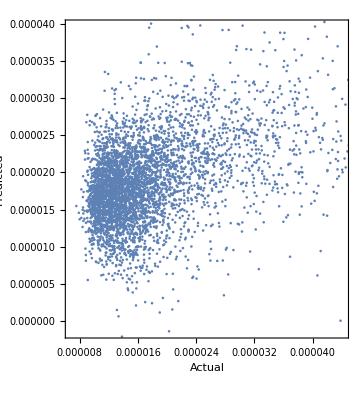

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
Minimize[
lm["BestFit"],
Symbol[#]&/@freeVars
]
```

NMinimize::ubnd: The problem is unbounded.

{-∞,{L1PhaseSet→Indeterminate,L2PhaseSet→Indeterminate,Q0FFkG→Indeterminate,Q1EkG→Indeterminate,Q1FFkG→Indeterminate,Q2EkG→Indeterminate,Q2FFkG→Indeterminate,Q3EkG→Indeterminate,Q3FFkG→Indeterminate,Q4EkG→Indeterminate,Q4FFkG→Indeterminate,Q5EkG→Indeterminate,Q5FFkG→Indeterminate,Q6EkG→Indeterminate,S1ELkG→Indeterminate,S1ERkG→Indeterminate,S2ELkG→Indeterminate,S2ERkG→Indeterminate,S3ELkG→Indeterminate,S3ERkG→Indeterminate}}

*facepalm* It’s a linear model, obviously it’s unbounded

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
L1PhaseSet | 1 | 6.01905×10^-8 | 6.01905×10^-8 | 477.627 | 1.10277×10^-100
L2PhaseSet | 1 | 4.62846×10^-8 | 4.62846×10^-8 | 367.28 | 9.73416×10^-79
Q0FFkG | 1 | 1.61288×10^-8 | 1.61288×10^-8 | 127.986 | 2.81574×10^-29
Q1EkG | 1 | 1.13051×10^-8 | 1.13051×10^-8 | 89.7089 | 4.34415×10^-21
Q1FFkG | 1 | 2.11305×10^-8 | 2.11305×10^-8 | 167.676 | 1.12453×10^-37
Q2EkG | 1 | 4.32366×10^-9 | 4.32366×10^-9 | 34.3094 | 5.03832×10^-9
Q2FFkG | 1 | 2.7885×10^-9 | 2.7885×10^-9 | 22.1274 | 2.62834×10^-6
Q3EkG | 1 | 3.06874×10^-9 | 3.06874×10^-9 | 24.3512 | 8.31932×10^-7
Q3FFkG | 1 | 7.16451×10^-9 | 7.16451×10^-9 | 56.8522 | 5.65566×10^-14
Q4EkG | 1 | 5.82531×10^-10 | 5.82531×10^-10 | 4.62253 | 0.0316081
Q4FFkG | 1 | 5.80764×10^-9 | 5.80764×10^-9 | 46.0851 | 1.28048×10^-11
Q5EkG | 1 | 6.85042×10^-11 | 6.85042×10^-11 | 0.543598 | 0.460984
Q5FFkG | 1 | 6.90898×10^-9 | 6.90898×10^-9 | 54.8245 | 1.56636×10^-13
Q6EkG | 1 | 2.49278×10^-11 | 2.49278×10^-11 | 0.197808 | 0.656517
S1ELkG | 1 | 1.34356×10^-9 | 1.34356×10^-9 | 10.6615 | 0.00110213
S1ERkG | 1 | 9.21265×10^-9 | 9.21265×10^-9 | 73.1047 | 1.66574×10^-17
S2ELkG | 1 | 8.11468×10^-10 | 8.11468×10^-10 | 6.4392 | 0.0111966
S2ERkG | 1 | 8.68262×10^-10 | 8.68262×10^-10 | 6.88988 | 0.00869799
S3ELkG | 1 | 3.20801×10^-11 | 3.20801×10^-11 | 0.254564 | 0.613905
S3ERkG | 1 | 6.27969×10^-10 | 6.27969×10^-10 | 4.98309 | 0.0256455
Error | 4471 | 5.63435×10^-7 | 1.2602×10^-10 |  | 
Total | 4491 | 7.62108×10^-7 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVars,
Symbol[#]&/@freeVars
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];
```

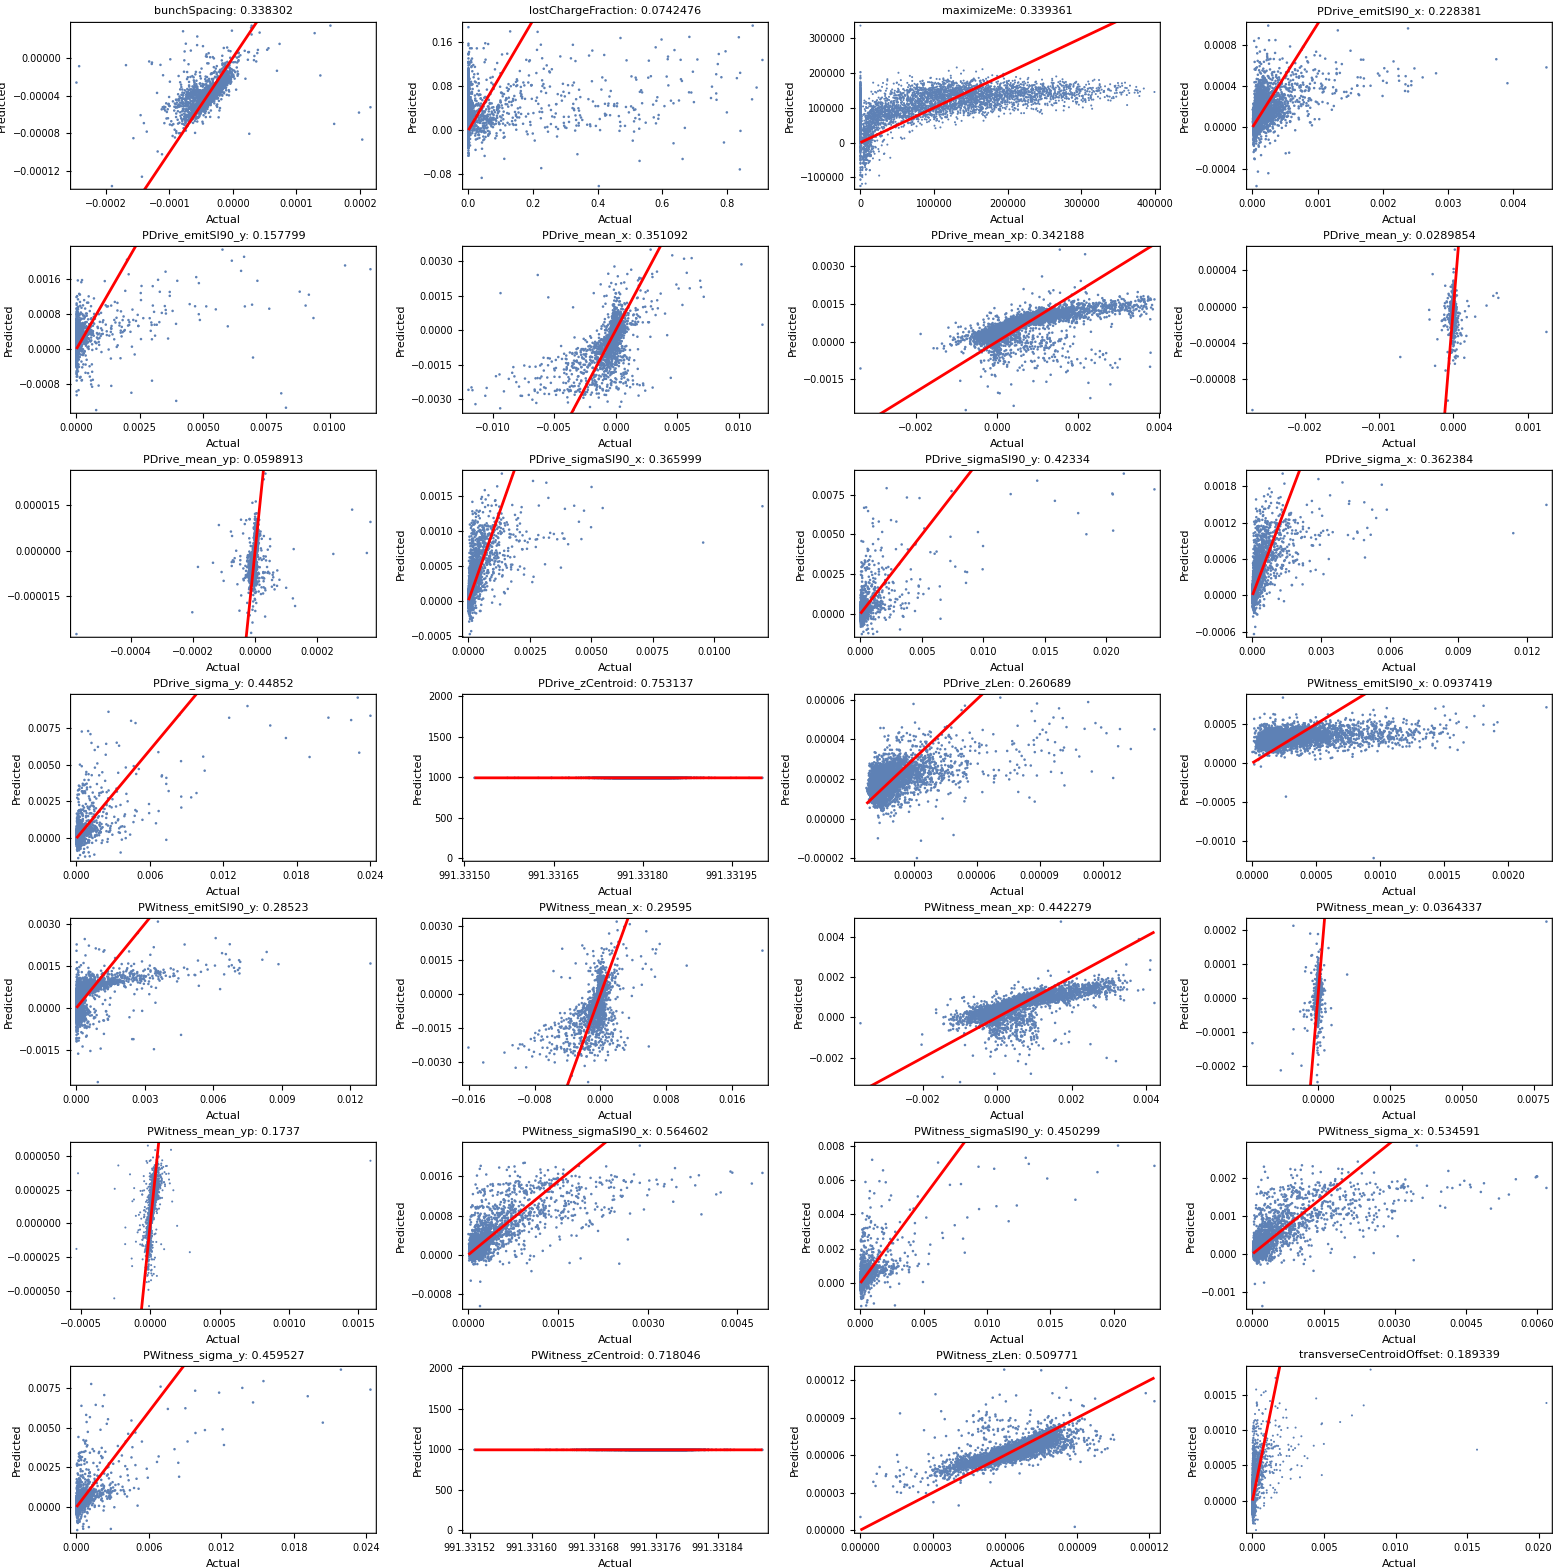

```mathematica
displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```